```mathematica
A=-Ω^2+1+δ^2;
B=2*1*δ;
Λ=-2(δ^2/(A √(1-(B/A)^2))-(A/(4*δ^2)-1)(1-1/(√(1-(B/A)^2))));(*Subscript[π, 22]*)
Ξ=-2(1+Ω^2/(A √(1-(B/A)^2)));(*Subscript[π, 33]*)
Φ=(ⅈ*Ω)/δ(1+(2*δ^2-A)/(A √(1-(B/A)^2)));(*Subscript[π, 23]*)
Ψ=-(ⅈ*Ω)/δ(1+(2*δ^2-A)/(A √(1-(B/A)^2)));(*Subscript[π, 32]*)
ψ=-2((A-A √(1-(B/A)^2))/(2δ)^2); (*Subscript[π, 11]*)
```

```mathematica
Δ=2*0.5;(*Rashba Spin Orbit Coupling*)
u=.3;(*Coulomb energy time density of states*)
δ=(α/Δ)/(1-u);(*Renormalized zeeman energy. Here α is α/Subscript[ϵ, F]*)
```

```mathematica
f1[α_]:=1+u/2(Λ+Ξ+u/2(Λ*Ξ-Φ*Ψ))(*Mode equation arising from Subscript[π, 22],Subscript[π, 33],Subscript[π, 23],Subscript[π, 32] *)
g1[α_]:=Ω^2-(1+δ)^2(*Particle hole excitation spectrum *)
g2[α_]:=Ω^2-(1-δ)^2(*Particle hole excitation spectrum *)
h[α_]:=1+u/2 ψ;(*Mode equation arising from Subscript[π, 11]*)
```

```mathematica
L1=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Max@Select[w,0<#<Re[√((1-δ)^2)]&]},{α,.02,(u*(1-u)*Δ)/(2(2-u)),0.002}],PlotStyle->{Thickness[0.005],Gray}];
L11=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Min@Select[w,0<#<Re[√((1-δ)^2)]&]},{α,.02,3,0.002}],PlotStyle->{Thickness[0.005],Blue}];
L3=ListLinePlot[Table[ {α,w=Ω/.NSolve[h[α]==0 ,Ω];Min@Select[w,Positive]},{α,.02,3,0.002}],PlotStyle->{Thickness[0.005],Red}];

(*ListLinePlot[Table[ {α,w=Ω/.NSolve[h[α]==0 ,Ω];Min@Select[w,Positive]},{α,0.01,.5,0.005}]]*)
```

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, 0 < #1 < Re[√(1 + Times[« 2 »])^2] &].

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, 0.` < #1 < Re[√(1.`  + Times[« 2 »])^2] &].

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, Positive].

General::stop: Further output of Select will be suppressed during this calculation.

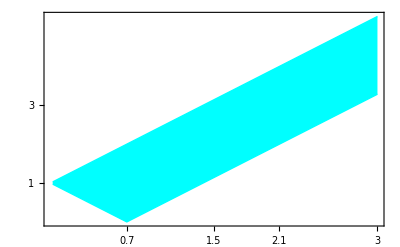

```mathematica
L4=Plot[{(1+δ),Abs[(1-δ)]},{α,.02,3},PlotRangePadding->0,PlotStyle->{Cyan,Cyan,Cyan},Filling->1->{2},FillingStyle->Cyan,Frame->True,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",16,SingleLetterItalics->True},FrameTicks->{{{1,3},Automatic},{{.70,1.5,2.1,3},Automatic}}]
```

```mathematica
L5=Graphics[{Thickness[0.005],Circle[{.1,.9},{.1,.2}]}];
```

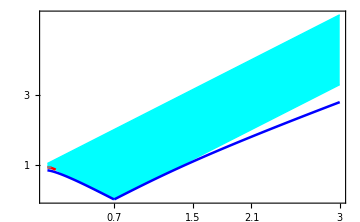

```mathematica
Show[L4,L11,L3,L1,Background->White,ImageSize->Medium]
```

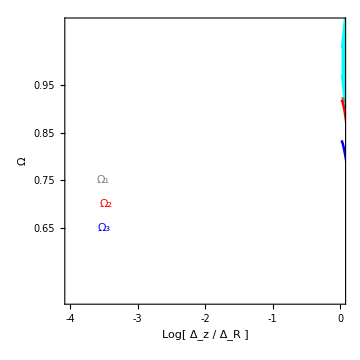

```mathematica
T2=Show[L4,L1,L11,L3,PlotRange->{{-4,0},{.5,1.08}},PlotRangePadding->-0.075,Frame-> True,FrameStyle->Directive[Black,Thickness@.005],FrameLabel->{"Log[ Δ_z / Δ_R ]","\!\( Ω / Δ_R \)"},BaseStyle->{FontFamily->"Arial",12,SingleLetterItalics->True},FrameTicks->{{{0.65,0.75,0.85,0.95},None},{{0,-1,-2,-3,-4},None}},Epilog->{Thickness[0.3],Gray,Text[" Ω_1",{-3.51,0.75}],Thickness[0.3],Red,Text["Ω_2  ",{-3.47,0.7}],
Thickness[0.3],Blue,Text[" Ω_3 ",{-3.5,0.65}]},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium]
```

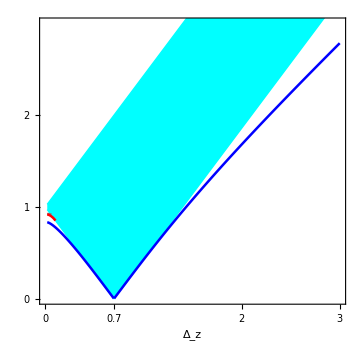

```mathematica
Show[L4,L1,L11,L3,PlotRange->{{.002,3},{0,3}},PlotRangePadding->-0.0004,Frame-> True,FrameStyle->Directive[Black,Thickness@.015],FrameLabel->{Framed[Style["\!\(Δ_z/Δ_R\)",14],FrameStyle->None,FrameMargins->1],None},BaseStyle->{FontFamily->"Arial",12,SingleLetterItalics->True},FrameTicks->{{{0,1, 2},None},{{0,0.7,2,3},None}},Background->White,AspectRatio->Automatic,PlotRangeClipping->True,ImageSize->Medium]
```

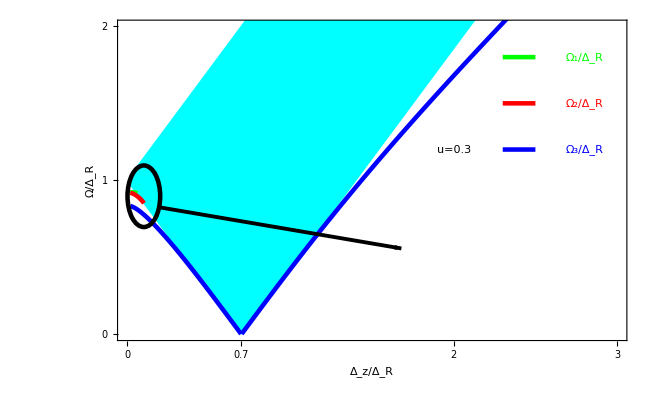

```mathematica
PlotExplorer
```

```mathematica
(*Magnified view of splited collective modes behavior.*)
```

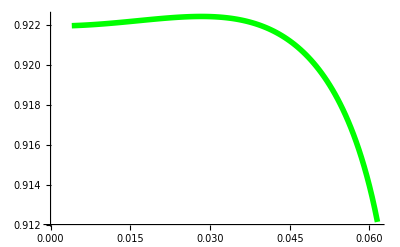

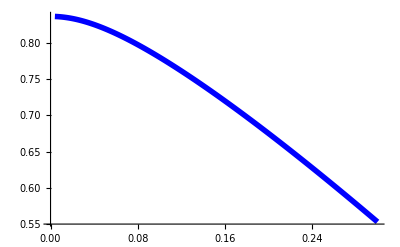

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, Positive].

General::stop: Further output of Select will be suppressed during this calculation.

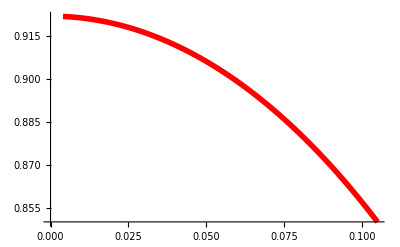

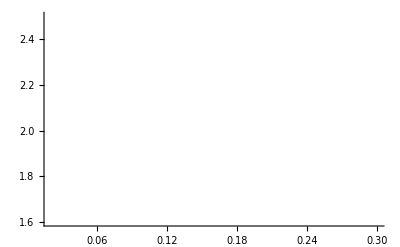

```mathematica
L1=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Max@Select[w,0<#<Re[√((1-δ)^2)]&]},{α,0.004,(u*(1-u)*Δ)/(2(2-u)),0.0005}],PlotStyle->{Thickness[0.01],Green}]
L11=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Min@Select[w,0<#<Re[√((1-δ)^2)]&]},{α,0.004,.30,0.0005}],PlotStyle->{Thickness[0.01],Blue}]
L3=ListLinePlot[Table[ {α,w=Ω/.NSolve[h[α]==0 ,Ω];Min@Select[w,Positive]},{α,0.004,.30,0.0005}],PlotStyle->{Thickness[0.01],Red}]

(*ListLinePlot[Table[ {α,w=Ω/.NSolve[h[α]==0 ,Ω];Min@Select[w,Positive]},{α,0.01,.5,0.005}]]*)
Show[L1,L11,L3,PlotRange->{{0.02,0.30},{1.6,2.5}},AxesOrigin->{0,0}]
```

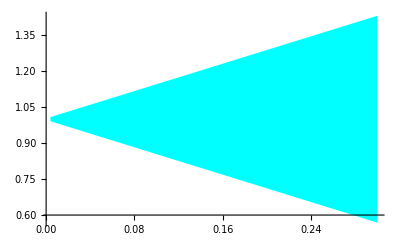

```mathematica
L4=Plot[{(1+δ),Abs[(1-δ)]},{α,.004,.30},PlotStyle->{Cyan,Cyan,Cyan},Filling->1->{2},FillingStyle->Cyan]
```

```mathematica
Show[L4,L11,L3,L1,PlotRange-> {{0.00,0.15},{.7,1}},PlotRangePadding->-0.004,AxesOrigin->{0,0},Frame-> True,FrameLabel->{"\!\(Δ_z/Δ_R\)","\!\(Ω/Δ_R\)"},BaseStyle->{FontFamily->"Arial",16,SingleLetterItalics->True},FrameTicks->{{{0.76,0.84, 0.92},Automatic},{{0.0,.03,0.06,0.09,.12,.15},Automatic}},Epilog->{Thickness[0.005],Green,Line[{{.010,.87},{.02,.87}}],Text[" Ω_1/Δ_R",{0.035,.87}],Thickness[0.005],Red,Line[{{.01,.8},{0.02,.8}}],Text["Ω_2/Δ_R  ",{0.035,.8}],
Thickness[0.005],Blue,Line[{{0.01,.74},{0.02,.74}}],Text[" Ω_3/Δ_R ",{.035,.74}],Thick,Black,Text[" u=0.3 ",{.02,.95}]}]
```

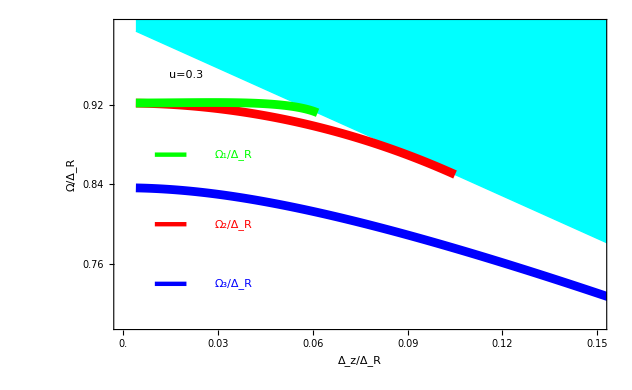

```mathematica
L5=Graphics[{Thickness[0.005],Circle[{.1,.9},{.1,.2}]}];
```

```mathematica
Show[L4,L1,L11,L3,L5,PlotRange->{{.002,3},{0,2}},Frame-> True,FrameLabel->{"\!\(Δ_z/Δ_R\)","\!\(Ω/Δ_R\)"},BaseStyle->{FontFamily->"Arial",20,SingleLetterItalics->True},FrameTicks->{{{0,2, 3},Automatic},{{0,0.7,1,1.5},Automatic}},Epilog->{Thickness[0.005],Green,Line[{{2.30,1.8},{2.50,1.8}}],Text[" Ω_1/Δ_R",{2.8,1.8}],Thickness[0.005],Red,Line[{{2.30,1.5},{2.50,1.5}}],Text["Ω_2/Δ_R  ",{2.8,1.5}],
Thickness[0.005],Blue,Line[{{2.30,1.2},{2.50,1.2}}],Text[" Ω_3/Δ_R ",{2.8,1.2}],Thick,Black,Text[" u=0.3 ",{2,1.2}]}, ImageSize->Scaled[0.585]]
```

```mathematica
(.3*.7)/1.7
```

0.123529

```mathematica
XX=(u(1-u)Δ)/(2(2-u))
```

0.0617647

```mathematica
zz=1*(1-u)
```

0.7

```mathematica
yy=Δ √(1-u)
```

0.83666

```mathematica
yy1=Δ √(1-u/2)
```

0.921954

```mathematica
LL11=(u(1-u)Δ)/4
```

0.0525

```mathematica
(*Plot*)
```